```mathematica
Parallelize[ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->30,ImageSize->250,FrameTicks->{{0,12,24,36},{0,12,24,36}}]&@data]
```

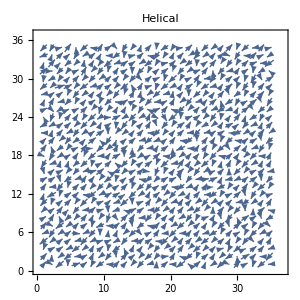

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@100000<>
"_T="<>ToString@#<>
"_J="<>ToString@1<>
"_B="<>ToString@0<>
"_D="<>ToString@2.5<>".vector"]]&@0.2;
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->30,ImageSize->300,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Helical",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&@data
```

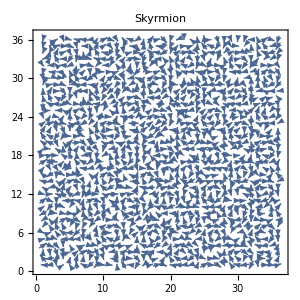

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@100000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString@2<>
"_D="<>ToString@2.5<>".vector"]];
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->300,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Skyrmion",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&@data
```

Parallelize::nopar1: (ListVectorPlot[#1/.{x_,y_,z_}→{x,y},VectorPoints→36,ImageSize→300,FrameTicksStyle→Directive[FontOpacity→0,FontSize→0],PlotLabel→Helical,LabelStyle→{FontFamily→Segoe UI,FontSize→12}]&)[data] cannot be parallelized; proceeding with sequential evaluation.

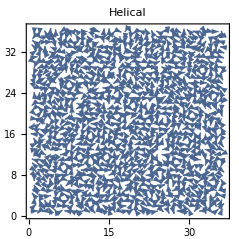

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@1000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString[-2]<>
"_D="<>ToString@2.5<>".vector"]];
Parallelize[
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->300,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Helical",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&@data]
```

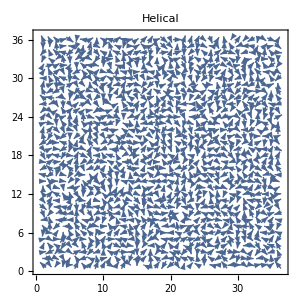

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@100000<>
"_T="<>ToString@1.5<>
"_J="<>ToString@1<>
"_B="<>ToString@2<>
"_D="<>ToString@2.5<>".vector"]];
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->300,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Helical",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&@data
```

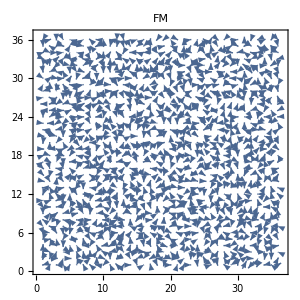

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@100000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString@4<>
"_D="<>ToString@2.5<>".vector"]];
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->300,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"FM",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&@data
```

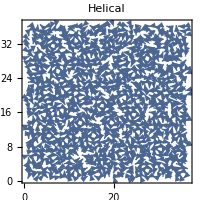
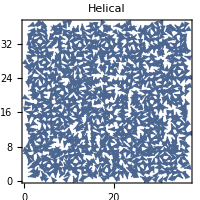
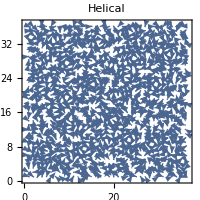
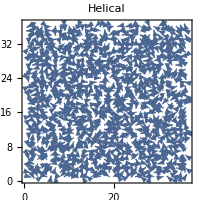
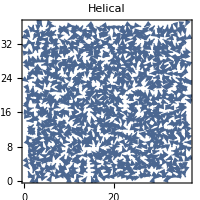
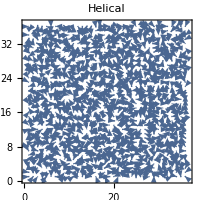

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Step="<>ToString@1000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString@#<>
"_D="<>ToString@2.5<>".vector"]&/@{3,3.2,3.4,3.6,3.8,4}];
Parallelize[
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->200,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Helical",LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]&/@data]
```

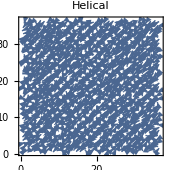
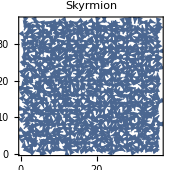
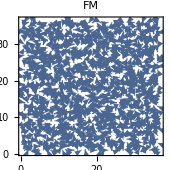

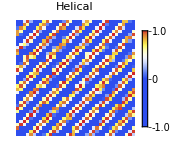

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Data\\Final vector plot\\Step="<>ToString@100000<>
"_T="<>ToString@0.2<>
"_J="<>ToString@1<>
"_B="<>ToString@0<>
"_D="<>ToString@2.5<>".vector"]];
ArrayPlot[Reverse[#,{2}]ᵀ/.{x_,y_,z_}->z,ImageSize->150,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Helical",LabelStyle->{FontFamily->"Segoe UI",FontSize->10},ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotLegends->Automatic]&@data
```

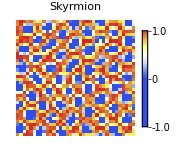

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Data\\Final vector plot\\Step="<>ToString@100000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString@2<>
"_D="<>ToString@2.5<>".vector"]];
ArrayPlot[Reverse[#,{2}]ᵀ/.{x_,y_,z_}->z,ImageSize->150,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"Skyrmion",LabelStyle->{FontFamily->"Segoe UI",FontSize->10},ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotLegends->Automatic]&@data
```

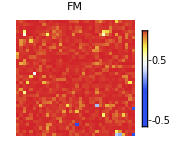

```mathematica
data=ToExpression[
Import[
"F:\\Project\\HeisenbergModel\\Debug\\Data\\Final vector plot\\Step="<>ToString@100000<>
"_T="<>ToString@0.1<>
"_J="<>ToString@1<>
"_B="<>ToString@4<>
"_D="<>ToString@2.5<>".vector"]];
ArrayPlot[Reverse[#,{2}]ᵀ/.{x_,y_,z_}->z,ImageSize->150,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],PlotLabel->"FM",LabelStyle->{FontFamily->"Segoe UI",FontSize->10},ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotLegends->Automatic]&@data
```

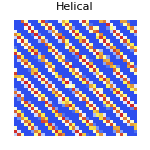
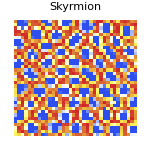
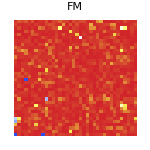
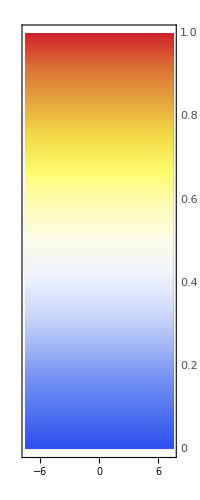

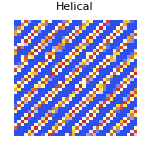
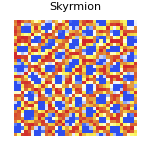
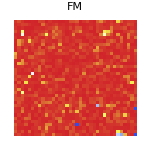
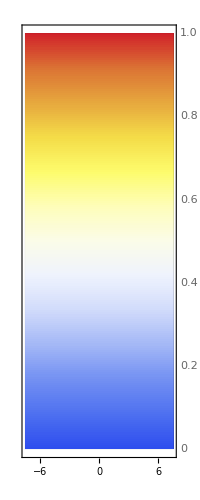

```mathematica
BarLegend["TemperatureMap",LabelStyle->{FontFamily->"Segoe UI",FontSize->10.5}]
```